```mathematica
SetDirectory["C:\\Users\\Dancsi\\petnica\\2014\\PedestrianSimulator\\paper\\logs"];
HighResPlot[fname_String]:=Module[{data=Import[fname, "Table"]//Flatten},
plot =ListLinePlot[data, Frame->True, FrameLabel->{"Generacija", "Vreme izlaska"}, Background->None,AxesStyle->White, FrameStyle->White,TicksStyle->White, PlotStyle->White];
Export[fname<>".eps", plot, "EPS"]];
HighResPlot["grid1.txt"]
HighResPlot["polygon2.txt"]
```

grid1.txt.eps

polygon2.txt.eps

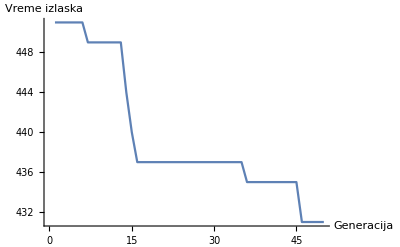

```mathematica
Show[%30,AxesStyle->White]
```

```mathematica
Show[%25,Background->None]
```

-Graphics-

```mathematica
Export["C:\\Users\\Dancsi\\petnica\\2014\\PedestrianSimulator\\paper\\Grid1plot.pdf",%25,"PDF"]
```

C:\Users\Dancsi\petnica\2014\PedestrianSimulator\paper\Grid1plot.pdf

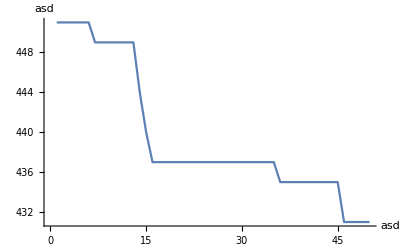

```mathematica
Show[%21,AxesLabel->{HoldForm[asd],HoldForm[asd]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```